# 2016.09.12 Fluorescence anisotropy of pyrene labeled TSG101cc titrated with ANTD of GR

## Jordan White

TSG101 was diluted 100 fold to 76nM. SLM48000 was used for all measurements. Excited at 345±4 nm with emission at 377±8 nm. HV of channel A held at 790--875 V. Temperature was ~17-20.baC. Room temperature controller was on.

The cuvette was incubated in the sample holder with the chiller running at 17.baC for about an hour. The dilution buffer was incubated in the ethylene glycol bath of the chiller at the same time.

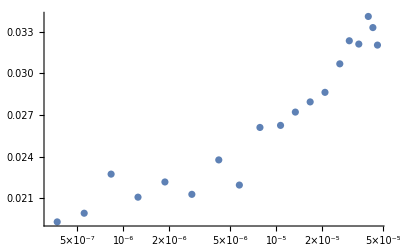

```mathematica
data=Transpose[{10^-9*{45912,42851,39994,34661,30039,26035,20828,16662,13330,10664,7820,5735,4206,2804,1869,1246,831,554,369},10^-2*{3.20497,3.3315,3.4118,3.2124,3.2362,3.0696,2.8637,2.7946,2.7211,2.62498,2.6101,2.19399,2.37566,2.127,2.21629,2.106496,2.27297,1.99059,1.927908}} ];(*Concentration of GR in Molar versus anisotropy*)
ListLogLinearPlot[data,PlotRange->All]
```

```mathematica
Export["20160912_ANTD-TSGcc.csv",N[data]]
```

20160912_ANTD-TSGcc.csv

#### One Binding Site:

```mathematica
fit[bu_,bb_,x_,kd_]:=bu*1/(1+x/kd)+bb*(x/kd)/(1+x/kd);
nlm=NonlinearModelFit[data,fit[bu,bb,x,kd],{{bu,0.02},{bb,0.06},{kd,5*10^-5}},x]
```

FittedModel[0.0200927/(1+37594.2 x)+(1554.87 x)/(1+37594.2 x)]

{bu→0.0200927,bb→0.0413593,kd→0.0000265998}

{0.000545405,0.00313178,9.01844×10^-6}

0.998444

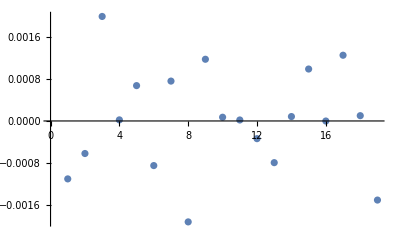

```mathematica
nlm["BestFitParameters"]
nlm["ParameterErrors"]
nlm["AdjustedRSquared"]
ListPlot[Reverse[nlm["FitResiduals"]]]
```

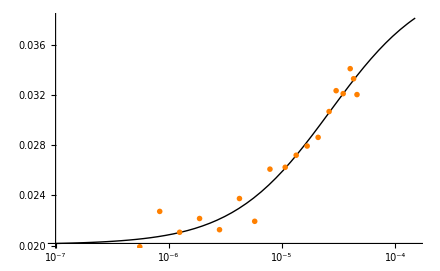

```mathematica
Show[LogLinearPlot[nlm[x],{x,1*10^-7,1.5*10^-4},PlotTheme->"Monochrome",PlotStyle->Thick],ListLogLinearPlot[data,PlotRange->All,PlotTheme->"Monochrome",PlotStyle->{Directive[PointSize[Medium],Orange]},AxesLabel->{"C3NTD (M)","Anisotropy"},PlotLabel->"Overlay of Data and Fit"]]
```

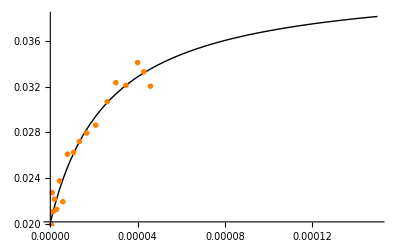

```mathematica
Show[Plot[nlm[x],{x,1*10^-7,1.5*10^-4},PlotTheme->"Monochrome",PlotStyle->Thick],ListPlot[data,PlotRange->All,PlotTheme->"Monochrome",PlotStyle->{Directive[PointSize[Medium],Orange]},AxesLabel->{"C3NTD (M)","Anisotropy"},PlotLabel->"Overlay of Data and Fit"]]
```

Calculation of interaction energy, by -RT*ln Ka  =  -RT*ln (Kd^-1):

```mathematica
-R*288.15*Log[(0.000026599847416648813)^-1]
```

-6031.63

#### Two Identical Binding Sites:

```mathematica
fit2[bu_,bb_,x_,kd_]:=bu*1/(1+2*x/kd+x^2/kd^2)+0.5*bb*(2*x/kd)/(1+2*x/kd+x^2/kd^2)+bb*(x^2/kd^2)/(1+2*x/kd+x^2/kd^2);
nlm2=NonlinearModelFit[data,fit2[bu,bb,x,kd],{{bu,0.02},{bb,0.06},{kd,1*10^-5}},x]
```

FittedModel[0.0210522/(1+257781. x+1.66128×10^10 x^2)+(«1»)/(«1»)+(6.4151×10^8 «1»)/(1+«18» x+«23» x^2)]

{bu→0.0210522,bb→0.0386155,kd→7.75852×10^-6}

{0.000589782,0.00197905,2.31656×10^-6}

0.998287

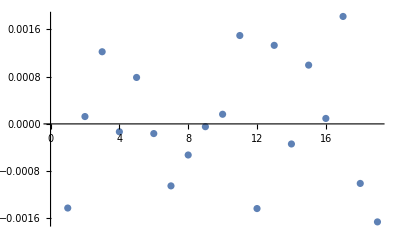

```mathematica
nlm2["BestFitParameters"]
nlm2["ParameterErrors"]
nlm2["AdjustedRSquared"]
ListPlot[nlm2["FitResiduals"]]
```

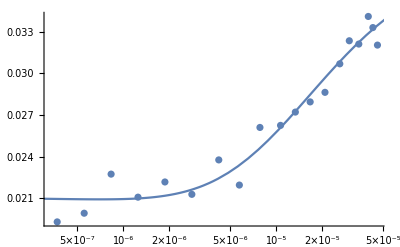

```mathematica
Show[ListLogLinearPlot[data,PlotRange->All],LogLinearPlot[nlm2[x],{x,1*10^-7,1.5*10^-4}]]
```

#### Two Dependent binding sites:

```mathematica
fit3[bu_,bb_,x_,kd1_,kd2_]:=bu*1/(1+2*x/kd1+x^2/kd2^2)+0.5*bb*(2*x/kd1)/(1+2*x/kd1+x^2/kd2^2)+bb*(x^2/kd2^2)/(1+2*x/kd1+x^2/kd2^2);
nlm3=NonlinearModelFit[data,fit3[bu,bb,x,kd1,kd2],{{bu,0.02},{bb,0.06},{kd1,1*10^-5},{kd2,2*10^-5}},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[-0.394389/(1+8.16849×10^8 x+2.75718×10^13 x^2)+(«21» x)/(1+«1»«1»«23» «1»)+(«23» x^2)/(1+«21» x+«23» x^2)]

{bu→-0.394389,bb→0.0416151,kd1→2.44843×10^-9,kd2→1.90444×10^-7}

{416.419,0.00504473,2.46534×10^-6,0.0000959388}

0.998402

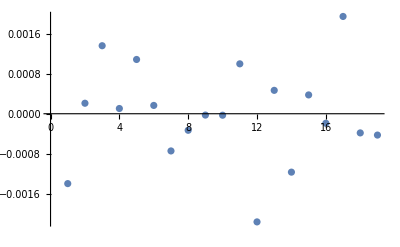

```mathematica
nlm3["BestFitParameters"]
nlm3["ParameterErrors"]
nlm3["AdjustedRSquared"]
ListPlot[nlm3["FitResiduals"]]
```

Global Fitting of this data and data from 2016-7-27 and 2016-8-9

## Set up:

2016-7-27

```mathematica
data2=Transpose[{10^-9*{26037,24177,20723,17763,13957,10966,8616,6154,4396,2826,1816,1168,751,483},10^-2*{3.4519,3.2665,3.17925,3.2805,3.01196,2.8868,2.7793,2.5226,2.41355,2.47097,2.2725,2.19495,2.0447,2.2104}} ];(*Concentration of GR in Molar versus anisotropy*)
```

2016-8-9

```mathematica
data3=Transpose[{10^-9*{45243,42011,39011,36224,31049,26614,22812,17923,14083,11065,8694,6209.9,4436,3168,1584,792,396},10^-2*{3.08298,3.0431,2.9311,2.92431,3.108698,3.2066,2.9159,2.7563,2.6439,2.3358,2.5754,2.3248,2.3313,2.235,1.97011,2.0038,1.90312}} ];(*Concentration of GR in Molar versus anisotropy*)
```

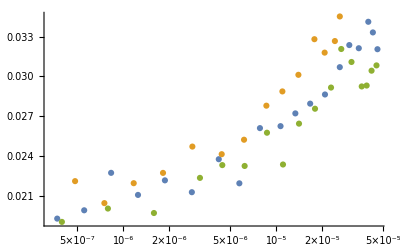

```mathematica
ListLogLinearPlot[{data,data2,data3},PlotRange->All]
```

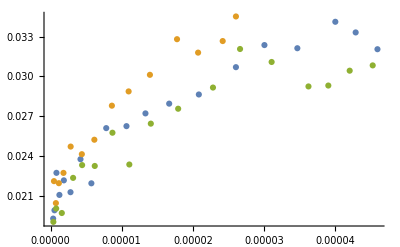

```mathematica
ListPlot[{data,data2,data3},PlotRange->All]
```

Now join the datasets and add some dummy variables to keep track of each dataset.

```mathematica
dataGlobal=Join[data/.{x_,y_}->{0,x,y},
data2/.{x_,y_}->{1,x,y},
data3/.{x_,y_}->{2,x,y}];
```

Below is our basic fitting function. It needs to be built up to accommodate the dummy variables.

```mathematica
fit[bu_,bb_,x_,kd_]:=bu*1/(1+x/kd)+bb*(x/kd)/(1+x/kd);
```

```mathematica
fitmodel[x_,bu_,bb0_,bb1_,bb2_,kd_,set_]:=Which[set==0,Evaluate@fit[bu,bb0,x,kd],
set==1,Evaluate@fit[bu,bb1,x,kd],
set==2,Evaluate@fit[bu,bb2,x,kd]];
```

The global model allows each fully bound baseline to fit individually, but the Kd and unbound baselines are shared.

## The fit:

```mathematica
globalFit=NonlinearModelFit[dataGlobal,fitmodel[x,bu,bb0,bb1,bb2,kd,set],{{bu,0.02},{bb0,0.04},{bb1,0.04},{bb2,0.04},{kd,2*10^-5}},{set,x}]
```

FittedModel[«1»]

{bu→0.0199553,bb0→0.0392839,bb1→0.0455281,bb2→0.0363539,kd→0.0000209055}

{0.000384168,0.00172534,0.00288245,0.00146867,4.66579×10^-6}

0.998359

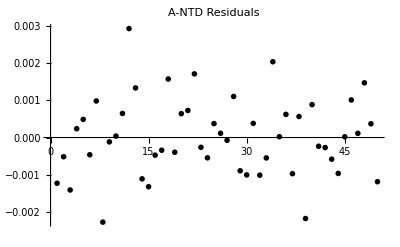

-9.39739×10^-6

```mathematica
globalFit["BestFitParameters"]
globalFit["ParameterErrors"]
globalFit["AdjustedRSquared"]
ListPlot[Reverse[globalFit["FitResiduals"]],PlotTheme->"Monochrome",PlotLabel->"A-NTD Residuals"]
globalFit["ParameterErrors"][[5]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[globalFit["Response"]]-Length[globalFit["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

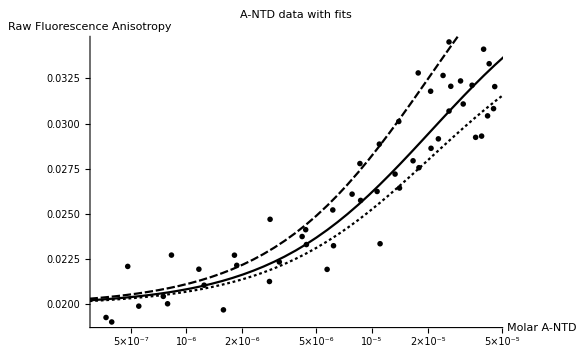

```mathematica
Show[ListLogLinearPlot[{data,data2,data3},PlotRange->All,PlotTheme->"Monochrome",PlotLabel->"A-NTD data with fits",AxesLabel->{"Molar A-NTD","Raw Fluorescence Anisotropy"}],LogLinearPlot[{fit[bu,bb0,x,kd]/.globalFit["BestFitParameters"],fit[bu,bb1,x,kd]/.globalFit["BestFitParameters"],fit[bu,bb2,x,kd]/.globalFit["BestFitParameters"]},{x,10^-7,6*10^-5},PlotTheme->"Monochrome"]]
```

Normalize the A data to the fraction bound: (data - unbound baseline) / (bound baseline - unbound baseline)

```mathematica
data1Anorm=Transpose[{Transpose[data][[1]],(Transpose[data][[2]]-0.019955287294822946)/(0.03928388550863731-0.019955287294822946)}];
data2Anorm=Transpose[{Transpose[data2][[1]],(Transpose[data2][[2]]-0.019955287294822946)/(0.04552814770361276-0.019955287294822946)}];
data3Anorm=Transpose[{Transpose[data3][[1]],(Transpose[data3][[2]]-0.019955287294822946)/(0.03635390082441098-0.019955287294822946)}];
```

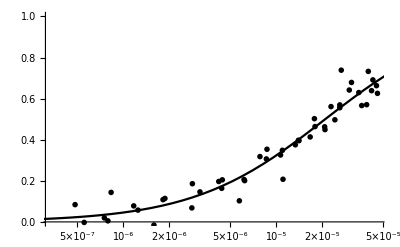

```mathematica
aGlobalNorm=Flatten[{data1Anorm,data2Anorm,data3Anorm},1];
Show[ListLogLinearPlot[aGlobalNorm,PlotTheme->"Monochrome",PlotRange->{Automatic,{0,1}}],LogLinearPlot[(x/0.00002090547938982087)/(1+x/0.00002090547938982087),{x,10^-7,1.7*10^-4},PlotTheme->"Monochrome"]]
```

```mathematica
Export["A_GlobalDATA-Normalized.csv",N[aGlobalNorm]]
```

A_GlobalDATA-Normalized.csv

```mathematica
normResiduals=Transpose[{Transpose[aGlobalNorm][[1]],Transpose[aGlobalNorm][[2]]-(Transpose[aGlobalNorm][[1]]/0.00002090547938982087)/(1+Transpose[aGlobalNorm][[1]]/0.00002090547938982087)}];
```

```mathematica
Export["A-GlobalResiduals-NormdDATA.csv",N[normResiduals]]
```

A-GlobalResiduals-NormdDATA.csv